Fixpunkte des Micropillar Lasersystems mit Feedback (Ν ist hier ein griechisches Nu):

```mathematica
Solve[{0==(Ν S)/(1+T)-S/τs,0==(J0+κ S-Ν)/τn-(Ν S)/(1+T),0==(cs S-T)/τt},{S,Ν,T}]
```

{{S→0,Ν→J0,T→0},{S→(-1+J0 τs)/(cs+τn-κ τs),Ν→(τn+cs J0 τs-κ τs)/(τs (cs+τn-κ τs)),T→(-cs+cs J0 τs)/(cs+τn-κ τs)}}

Jacobi-Matrix mit Berücksichtigung des zeitverzögerten Signals Σ:=S[t-τ]:

```mathematica
A=FullSimplify[D[{(Ν S)/(1+T)-S/τs,(J0+κ Σ-Ν)/τn-(Ν S)/(1+T),(cs S-T)/τt},{{S,Ν,T}}]];
MatrixForm[A]
```

(Ν/(1+T)-1/τs | S/(1+T) | -(S Ν)/(1+T)^2
-Ν/(1+T) | -(1+T+S τn)/(τn+T τn) | (S Ν)/(1+T)^2
cs/τt | 0 | -1/τt)

Jacobi-Matrix mit Ableitungen nach den zeitverzögerten Größen Σ=S[t-τ], ν=Ν[t-τ] und Τ(Tau)=T[t-τ]:

```mathematica
B=FullSimplify[D[{(Ν S)/(1+T)-S/τs,(J0+κ Σ-Ν)/τn-(Ν S)/(1+T),(cs S-T)/τt},{{Σ,ν,Τ}}]];
MatrixForm[B]
```

(0 | 0 | 0
κ/τn | 0 | 0
0 | 0 | 0)

Einsetzen des zweiten Fixpunktes x_2^* in A:

```mathematica
S=(τs J0-1)/(cs+τn-κ τs);Ν=(τn+τs(cs J0-κ))/(τs (cs+τn-κ τs));T=(cs (τs J0-1))/(cs+τn-κ τs);
FullSimplify[MatrixForm[A]]
```

(0 | (-1+J0 τs)/(τn+cs J0 τs-κ τs) | (1-J0 τs)/(τs (τn+cs J0 τs-κ τs))
-1/τs | ((κ-J0 (cs+τn)) τs)/(τn (τn+cs J0 τs-κ τs)) | (-1+J0 τs)/(τs (τn+cs J0 τs-κ τs))
cs/τt | 0 | -1/τt)

Bestimmung der Eigenvektoren v=(x,y,z) und reellen Eigenwerte Λ durch Lösen der transzendenten inhomogenen Eigenwertgleichung des Systems mit Zeitverzögerung bei Vorgabe eines realen Startwertes für Λ. Da es drei Gleichungen (3x3 Matrix) und vier Variablen (x, y, z, Λ) sind, wird angenommen x sei nicht Null und auf x=1 normiert. Bei dem gewählten Parametersatz liegt die Instabilitätsgrenze κ≈1. (τ_S, τ_Ν, τ_T, τ in Nanosekunden):

```mathematica
S=.;Ν=.;T=.;τs=.;τn=.;τt=.;τ=.;β=.;κ=.;cs=.;J0=.;
A=FullSimplify[D[{(Ν S)/(1+T)-S/τs,(J0+κ Σ-Ν)/τn-(Ν S)/(1+T),(cs S-T)/τt},{{S,Ν,T}}]];
B=FullSimplify[D[{(Ν S)/(1+T)-S/τs,(J0+κ Σ-Ν)/τn-(Ν S)/(1+T),(cs S-T)/τt},{{Σ,ν,Τ}}]];
S=(τs J0-1)/(cs+τn-κ τs);Ν=(τn+τs(cs J0-κ))/(τs (cs+τn-κ τs));T=(cs (τs J0-1))/(cs+τn-κ τs);
β=0.01;
τs=10^-2;
τn=10^-2;
τt=6*10^3;
τ=610;
cs=0.08;
J0=150;
v={1,y,z};

list=Range[0];
step=0.01;
ProgressIndicator[Dynamic[κ],{0,9-step}]

λ=-0.001;
Do[s=FindRoot[Λ v==A.v+B.v Exp[-Λ τ],{{y,1},{z,0},{Λ,Max[0,λ]+0.01}},MaxIterations->Infinity];
λ=s[[3,2]];
list=Flatten[Append[list,{κ,λ}]],
{κ,0,9-step,step}]

realew=Partition[list,2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

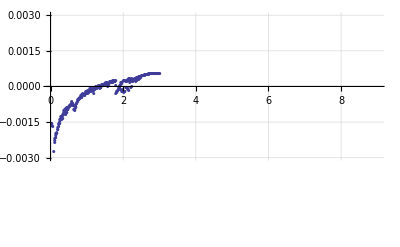

```mathematica
ListPlot[realew,AxesLabel->{"κ","Λ(κ)"},PlotRange->{{0,9},{-0.003,0.003}},PlotMarkers->{●,2},GridLines->Automatic]
```

Berechnung der komplexen Eigenwerte bei vier verschiedenen komplexen Startwerten, wobei nur der Imaginärteil verändert wird, der die Oszillationsfrequenz des Eigenvektors beschreibt:

```mathematica
S=.;Ν=.;T=.;τs=.;τn=.;τt=.;τ=.;β=.;κ=.;cs=.;J0=.;
A=FullSimplify[D[{(Ν S)/(1+T)-S/τs,(J0+κ Σ-Ν)/τn-(Ν S)/(1+T),(cs S-T)/τt},{{S,Ν,T}}]];
B=FullSimplify[D[{(Ν S)/(1+T)-S/τs,(J0+κ Σ-Ν)/τn-(Ν S)/(1+T),(cs S-T)/τt},{{Σ,ν,Τ}}]];
S=(τs J0-1)/(cs+τn-κ τs);Ν=(τn+τs(cs J0-κ))/(τs (cs+τn-κ τs));T=(cs (τs J0-1))/(cs+τn-κ τs);
β=0.01;
τs=10^-2;
τn=10^-2;
τt=6*10^3;
τ=610;
cs=0.08;
J0=150;
v={1,y,z};

l1=l2=l3=l4=m1=m2=m3=m4=n1=n2=n3=n4=Range[0];
step=0.01;
min=0;
max=9-step;
ProgressIndicator[Dynamic[κ],{min,max}]

λ=-0.001;
Do[s=FindRoot[Λ v==A.v+B.v Exp[-Λ τ],{{y,1},{z,0},{Λ,Max[0,Re[λ]]+0.01}},MaxIterations->Infinity];
λ=s[[3,2]];
l1=Flatten[Append[l1,{κ,Re[λ]}]];
m1=Flatten[Append[m1,{κ,Im[λ]}]];
n1=Flatten[Append[n1,{Re[λ],Im[λ]}]],
{κ,min,max,step}]
κre1=Partition[l1,2];
κim1=Partition[m1,2];
reim1=Partition[n1,2];

Do[s=FindRoot[Λ v==A.v+B.v Exp[-Λ τ],{{y,1},{z,0},{Λ,-0.005-30I}},MaxIterations->Infinity];
λ=s[[3,2]];
l2=Flatten[Append[l2,{κ,Re[λ]}]];
m2=Flatten[Append[m2,{κ,Im[λ]}]];
n2=Flatten[Append[n2,{Re[λ],Im[λ]}]],
{κ,min,max,step}]
κre2=Partition[l2,2];
κim2=Partition[m2,2];
reim2=Partition[n2,2];

Do[s=FindRoot[Λ v==A.v+B.v Exp[-Λ τ],{{y,1},{z,0},{Λ,-0.001-60I}},MaxIterations->Infinity];
λ=s[[3,2]];
l3=Flatten[Append[l3,{κ,Re[λ]}]];
m3=Flatten[Append[m3,{κ,Im[λ]}]];
n3=Flatten[Append[n3,{Re[λ],Im[λ]}]],
{κ,min,max,step}]
κre3=Partition[l3,2];
κim3=Partition[m3,2];
reim3=Partition[n3,2];

Do[s=FindRoot[Λ v==A.v+B.v Exp[-Λ τ],{{y,1},{z,0},{Λ,-0.001-100I}},MaxIterations->Infinity];
λ=s[[3,2]];
l4=Flatten[Append[l4,{κ,Re[λ]}]];
m4=Flatten[Append[m4,{κ,Im[λ]}]];
n4=Flatten[Append[n4,{Re[λ],Im[λ]}]],
{κ,min,max,step}]

κre4=Partition[l4,2];
κim4=Partition[m4,2];
reim4=Partition[n4,2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

In der Darstellung des Real- und Imaginärteils der Eigenwerte erhöht sich κ in Richtung höherer Realteile. In Richtung niedrigerer Realteile liegen die Eigenwerte nicht mehr so dicht, da κ und damit der Delay-Term gegen Null läuft. Der Phasenraum für Delay-Differentialgleichungssysteme ist unendlich-dimensional, während er für das Micropillar Lasersystem ohne Delay-Term dreidimensional ist. Für hinreichend kleine κ verschwinden die Eigenwerte im Unendlichen (und spielen daher keine Rolle mehr) und für κ->0 existieren drei Eigenwerte:

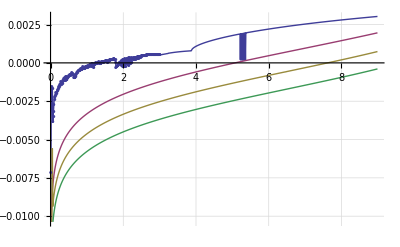

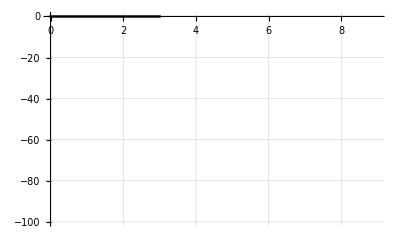

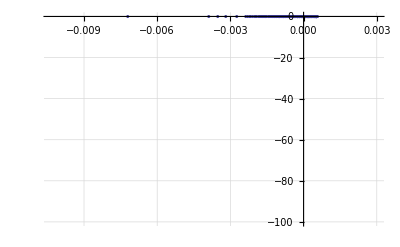

```mathematica
ListLinePlot[{κre1,κre2,κre3,κre4},AxesLabel->{"κ","Re(λ(κ))"},PlotMarkers->{●,2}]
ListPlot[{κim1,κim2,κim3,κim4},AxesLabel->{"κ","Im(λ(κ))"},PlotMarkers->{●,2}]
ListPlot[{reim1,reim2,reim3,reim4},AxesLabel->{"Re(λ)","Im(λ(κ))"},PlotMarkers->{●,2}]
```

Eigenwertspektrum: Durchlaufen des Imaginärteils des Eigenwertes als Startwert zur Ermittlung der komplexen Eigenwerte zu einem gesetzten κ:

```mathematica
S=.;Ν=.;T=.;τs=.;τn=.;τt=.;τ=.;β=.;κ=.;cs=.;J0=.;
A=FullSimplify[D[{(Ν S)/(1+T)-S/τs,(J0+κ Σ-Ν)/τn-(Ν S)/(1+T),(cs S-T)/τt},{{S,Ν,T}}]];
B=FullSimplify[D[{(Ν S)/(1+T)-S/τs,(J0+κ Σ-Ν)/τn-(Ν S)/(1+T),(cs S-T)/τt},{{Σ,ν,Τ}}]];
S=(τs J0-1)/(cs+τn-κ τs);Ν=(τn+τs(cs J0-κ))/(τs (cs+τn-κ τs));T=(cs (τs J0-1))/(cs+τn-κ τs);
τs=10^-2;
τn=10^-2;
τt=6*10^3;
τ=610;
cs=0.08;
J0=150;
v={1,y,z};

a=Range[0];
b=Range[0];
c=Range[0];
min=-0.20;
max=0.20;
step=0.0001;
ProgressIndicator[Dynamic[im],{min,max}]

κ=0.5;
Do[s=FindRoot[Λ v==A.v+B.v Exp[-Λ τ],{{y,1},{z,0},{Λ,0-im I}},MaxIterations->Infinity];
λ=s[[3,2]];
a=Flatten[Append[a,{Re[λ],Im[λ]}]],
{im,min,max,step}]

κ=1;
Do[s=FindRoot[Λ v==A.v+B.v Exp[-Λ τ],{{y,1},{z,0},{Λ,0-im I}},MaxIterations->Infinity];
λ=s[[3,2]];
b=Flatten[Append[b,{Re[λ],Im[λ]}]],
{im,min,max,step}]

κ=2;
Do[s=FindRoot[Λ v==A.v+B.v Exp[-Λ τ],{{y,1},{z,0},{Λ,0-im I}},MaxIterations->Infinity];
λ=s[[3,2]];
c=Flatten[Append[c,{Re[λ],Im[λ]}]],
{im,min,max,step}]

reim05=Partition[a,2];
reim1=Partition[b,2];
reim2=Partition[c,2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

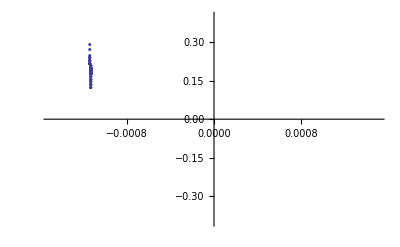

```mathematica
ListPlot[{reim05,reim1,reim2},AxesOrigin->{0,0},AxesLabel->{"Re(λ)","Im(λ)"},PlotRange->{{-0.0015,0.0015},{-0.4,0.4}},PlotMarkers->{●,2},Epilog->{Text["κ = 0.5",Scaled[{.06,.65}]],Text["κ = 1",Scaled[{.44,.65}]],Text["κ = 2",Scaled[{.93,.65}]]}]
```

Eigenwertspektrum: herausgezoomt

```mathematica
a=Range[0];
b=Range[0];
c=Range[0];
min=-150;
max=150;
step=0.1;
ProgressIndicator[Dynamic[im],{min,max}]

κ=0.5;
Do[s=FindRoot[Λ v==A.v+B.v Exp[-Λ τ],{{y,1},{z,0},{Λ,0-im I}},MaxIterations->Infinity];
λ=s[[3,2]];
a=Flatten[Append[a,{Re[λ],Im[λ]}]],
{im,min,max,step}]

κ=1;
Do[s=FindRoot[Λ v==A.v+B.v Exp[-Λ τ],{{y,1},{z,0},{Λ,0-im I}},MaxIterations->Infinity];
λ=s[[3,2]];
b=Flatten[Append[b,{Re[λ],Im[λ]}]],
{im,min,max,step}]

κ=2;
Do[s=FindRoot[Λ v==A.v+B.v Exp[-Λ τ],{{y,1},{z,0},{Λ,0-im I}},MaxIterations->Infinity];
λ=s[[3,2]];
c=Flatten[Append[c,{Re[λ],Im[λ]}]],
{im,min,max,step}]

reim05=Partition[a,2];
reim1=Partition[b,2];
reim2=Partition[c,2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

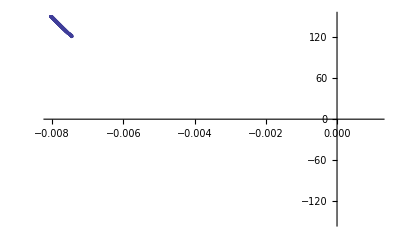

```mathematica
ListPlot[{reim05,reim1,reim2},AxesOrigin->{0,0},AxesLabel->{"Re(λ)","Im(λ)"},PlotMarkers->{●,2},Epilog->{Text["κ = 0.5",Scaled[{.10,.76}]],Text["κ = 1",Scaled[{.29,.86}]],Text["κ = 2",Scaled[{.43,.86}]]}]
```

Zeitverläufe S(t), Ν(t) und T(t), Phasenraumportrait S(Ν) mit Berücksichtigung des Terms für spontane Emission und Begrenzung des Feedbacks. Das Micropillar Lasersystem mit Zeitverzögerung scheint ein “steifes” Problem sein. Deswegen “BDF”=Backwards Differentiation Formula, StiffnessSwitching oder ImplicitRungeKutta zum numerischen Integrieren nutzen:

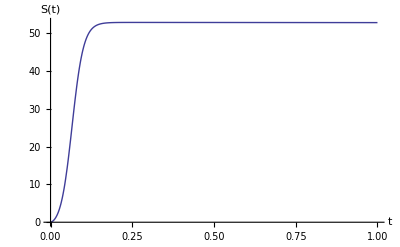

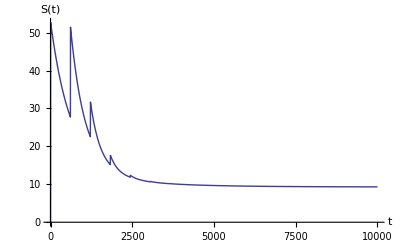

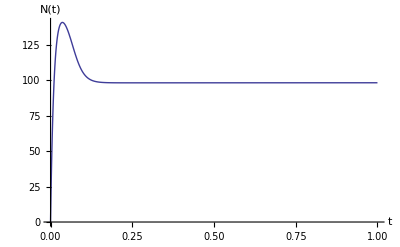

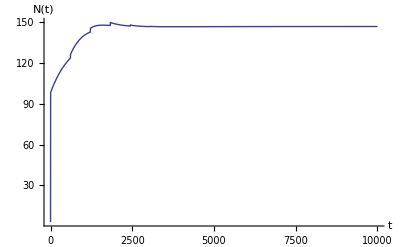

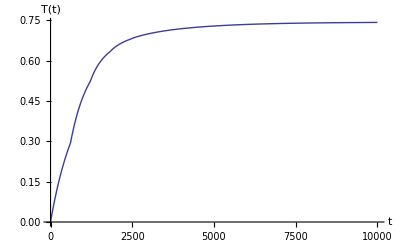

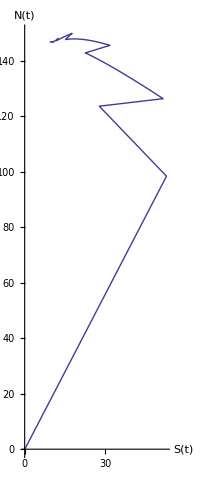

-Graphics3D-

```mathematica
S=.;Ν=.;T=.;τs=.;τn=.;τt=.;τ=.;β=.;κ=.;cs=.;J0=.;
β=0.01;
τs=10^-2;
τn=10^-2;
τt=6*10^3;
τ=610;
cs=0.08;
J0=150;
Jfbmax=200;
κ=0.5;
tmax=10000;
intstep=0.1;

Sfix=(τs J0-1)/(cs+τn-κ τs);Νfix=(τn+τs(cs J0-κ))/(τs (cs+τn-κ τs));Tfix=(cs (τs J0-1))/(cs+τn-κ τs);
Sdev=-0.99 Sfix;
Νdev=-Νfix;
Tdev=-Tfix;

s=NDSolve[{S'[t]==(Ν[t] S[t])/(1+T[t])-S[t]/τs+(β Ν[t])/τn,Ν'[t]==(J0+Min[Jfbmax,κ S[t-τ]]-Ν[t])/τn-(Ν[t] S[t])/(1+T[t]),T'[t]==(cs S[t]-T[t])/τt,{S[t/;t≤0]==Sfix+Sdev,Ν[t/;t≤0]==Νfix+Νdev,T[t/;t≤0]==Tfix+Tdev}},{S,Ν,T},{t,0,tmax},StartingStepSize->intstep,Method->"BDF",MaxSteps->Infinity];
Plot[Evaluate[S[t]/.s],{t,0,tmax/10000},AxesLabel->{"t","S(t)"},PlotRange->All]
Plot[Evaluate[S[t]/.s],{t,0,tmax},AxesLabel->{"t","S(t)"},PlotRange->All]
Plot[Evaluate[Ν[t]/.s],{t,0,tmax/10000},AxesLabel->{"t","N(t)"},PlotRange->All]
Plot[Evaluate[Ν[t]/.s],{t,0,tmax},AxesLabel->{"t","N(t)"},PlotRange->All]
Plot[Evaluate[T[t]/.s],{t,0,tmax},AxesLabel->{"t","T(t)"},PlotRange->All]
ParametricPlot[Evaluate[{S[t],Ν[t]}/.s],{t,0,tmax},AxesLabel->{"S(t)","Ν(t)"},PlotRange->All]
ParametricPlot3D[Evaluate[{S[t],Ν[t],300T[t]}/.s],{t,0,tmax},AxesLabel->{"S(t)","Ν(t)","T(t)"},PlotRange->All]
```

Input-Output Kurve:

```mathematica
S=.;Ν=.;T=.;τs=.;τn=.;τt=.;τ=.;β=.;κ=.;cs=.;J0=.;
β=0.01;
τs=10^-2;
τn=10^-2;
τt=6*10^3;
τ=610;
cs=0.08;
κ=0.5;
Jfbmax=200;
tmax=10000;
Jmax=400;
intstep=0.1;
iostep=0.1;
Sfix=0.01;Νfix=J0;Tfix=0;
Sdev=-0.99 Sfix;
Νdev=-Νfix;
Tdev=-Tfix;
a=Range[0];
ProgressIndicator[Dynamic[J0],{0,Jmax}]

Do[s=NDSolve[{S'[t]==(Ν[t] S[t])/(1+T[t])-S[t]/τs+(β Ν[t])/τn,Ν'[t]==(J0+Min[Jfbmax,κ S[t-τ]]-Ν[t])/τn-(Ν[t] S[t])/(1+T[t]),T'[t]==(cs S[t]-T[t])/τt,{S[t/;t≤0]==Sfix+Sdev,Ν[t/;t≤0]==Νfix+Νdev,T[t/;t≤0]==Tfix+Tdev}},{S,Ν,T},{t,0,tmax},StartingStepSize->intstep,Method->"BDF",MaxSteps->Infinity];a=Flatten[Append[a,{J0,Evaluate[S[tmax]/.s]}]],{J0,0,Jmax,iostep}];
io=Partition[a,2];
```

Input-Output Kurve für c_S=0:

```mathematica
S=.;Ν=.;τs=.;τn=.;β=.;κ=.;J0=.;
β=0.01;
τs=10^-2;
τn=10^-2;
τ=610;
κ=0.5;
Jfbmax=200;
tmax=10000;
Jmax=400;
step=0.1;
Sfix=0.01;Νfix=J0;
Sdev=-0.99 Sfix;
Νdev=-Νfix;
b=Range[0];

ProgressIndicator[Dynamic[J0],{0,Jmax}]
Do[s=NDSolve[{S'[t]==Ν[t] S[t]-S[t]/τs+(β Ν[t])/τn,Ν'[t]==(J0+Min[Jfbmax,κ S[t-τ]]-Ν[t])/τn-Ν[t] S[t],{S[t/;t≤0]==Sfix+Sdev,Ν[t/;t≤0]==Νfix+Νdev}},{S,Ν},{t,0,tmax}];b=Flatten[Append[b,{J0,Evaluate[S[tmax]/.s]}]],{J0,0,Jmax,step}];
iocs0=Partition[b,2];
```

NDSolve::ndcf: Repeated convergence test failure at t == 610.; unable to continue.

InterpolatingFunction::dmval: Input value {10000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndcf: Repeated convergence test failure at t == 610.; unable to continue.

InterpolatingFunction::dmval: Input value {10000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndcf: Repeated convergence test failure at t == 610.; unable to continue.

General::stop: Further output of NDSolve::ndcf will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {10000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

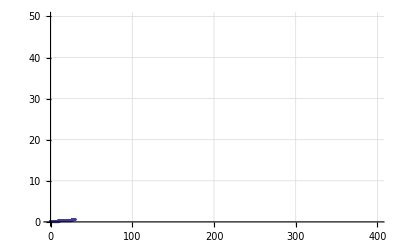

```mathematica
ListPlot[{io,iocs0},AxesLabel->{"J_0","S(J_0)"},PlotMarkers->{●,2},PlotRange->{{0,400},{0,50}},GridLines->Automatic,Epilog->{Text["κ = 0.5",Scaled[{.152,.94}]],Text["J_FB^max = 200",Scaled[{.13,.85}]],Text["c_S = 0.08",Scaled[{.82,.50}]],Text["c_S = 0",Scaled[{.33,.50}]]}]
```